```mathematica
Quit
```

```mathematica
<<"~/Github/1plus1d/OneFlavour.m"
```

```mathematica
mQ=4.23;n1=n2=n3=n4=0;
```

```mathematica
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=(g^2 Nc)/(2 π)*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
gglo=1;Nc=(β^2 2π)/g^2;(*ℂ denotes the interchange of final states.*)
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
Mn[n_][vals_]:=vals[[n+1]];

ω1S[s_][M1_,M2_,M3_,M4_]:=(-M1^2+M2^2+s-Sqrt[s] Sqrt[(M1^4+(M2^2-s)^2-2 M1^2 (M2^2+s))/s])/(M3^2-M4^2+s+Sqrt[s] Sqrt[(M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s]);
ω2S[s_][M1_,M2_,M3_,M4_]:=(-M3^2+M4^2+s-Sqrt[s] Sqrt[(M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s])/(M3^2-M4^2+s+Sqrt[s] Sqrt[(M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s]);
```

```mathematica
If[$OperatingSystem=="Windows",{dirglo="D:/Documents/2-d-data";},{dirglo="~/Documents/2-d-data";}];
```

```mathematica
ℐ1[ω1_,ω2_,opt:OptionsPattern[]][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2 (NIntegrate[(ω1 ω2 (ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ2'[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))))/((y-1) ω1+(1-x) ω2)^2,{x,0,1},{y,0,1},Evaluate[FilterRules[{opt},Options[NIntegrate]]]](*+(ω2 NIntegrate[(ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2])/(((ω1-(1-x) ω2) ((ω1-(1-x) ω2)/ω1-1))/ω1),{x,0,1}])/ω1*));
ℐ2[ω1_,ω2_,opt:OptionsPattern[]][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2 (NIntegrate[(ω1 (ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ3[x] (ϕ2[y] ϕ4[((y-1) ω1+ω2)/ω2]-ϕ2[x/ω1] ϕ4[(x-ω1+ω2)/ω2]-(y-x/ω1) (ϕ2'[x/ω1] ϕ4'[(x-ω1+ω2)/ω2]))))/(y ω1-x)^2,{x,0,1},{y,0,1},Evaluate[FilterRules[{opt},Options[NIntegrate]]]](*+NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ3[x] ϕ2[x/ω1] ϕ4[(x-ω1+ω2)/ω2])/((x (x/ω1-1))/ω1),{x,0,1}]/ω1*));
```

```mathematica
m1=mQ;m2=mQ;λ=10^-6;g=gglo;dir=dirglo;Nx=OptionValue[MatrixSize];
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
(*If[FileNames[filenameacc,dir,Infinity]=={},*)(*If[ChoiceDialog["Choose to use BSW method or to use the original solution suggested by 't Hooft, ",{"BSW method"->True,"Brute force integration"->False}],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];*)
filename=filenameacc;Determine=accDetermineϕ;
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[Global`x_],Boole[0<=Global`x<=1]ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[Global`x_],Boole[0<Global`x<1]ϕxB};
}
];
(*Set@@{ΦB[x_?NumberQ],If[0<x<1,ΦBi[x],Table[0,{n,Length@ϕxB}]]};*)
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[n3];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[n4];
(*Print[ϕ1[x]];*)
Mseq=Sequence[M1,M2,M3,M4];Si=If[n1+n2>=n3+n4,M1+M2,M3+M4];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
```

Wavefunction build complete.

M1=9.10387  M2=9.10387  M3=9.10387  M4=9.10387

```mathematica
ΦB[x][[1]]
```

2.00661 Boole[0≤x≤1] (0.343526 (1-x)^1.06207 x^0.937928+0.346584 (1-x)^0.937928 x^1.06207-0.841569 Sin[π x]+0.000042429 Sin[2 π x]+0.230083 Sin[3 π x]+9.86781×10^-6 Sin[4 π x]-0.0263305 Sin[5 π x]+4.64373×10^-6 Sin[6 π x]+0.000548951 Sin[7 π x]+3.68061×10^-6 Sin[8 π x])

```mathematica
ϕ2[x]=Boole[0<x<1]ϕ2[x]
```

2.00661 Boole[0<x<1]^2 (0.343526 (1-x)^1.06207 x^0.937928+0.346584 (1-x)^0.937928 x^1.06207-0.841569 Sin[π x]+0.000042429 Sin[2 π x]+0.230083 Sin[3 π x]+9.86781×10^-6 Sin[4 π x]-0.0263305 Sin[5 π x]+4.64373×10^-6 Sin[6 π x]+0.000548951 Sin[7 π x]+3.68061×10^-6 Sin[8 π x])

```mathematica
ϕ3[x]
```

2.00661 Boole[0<x<1] (0.343526 (1-x)^1.06207 x^0.937928+0.346584 (1-x)^0.937928 x^1.06207-0.841569 Sin[π x]+0.000042429 Sin[2 π x]+0.230083 Sin[3 π x]+9.86781×10^-6 Sin[4 π x]-0.0263305 Sin[5 π x]+4.64373×10^-6 Sin[6 π x]+0.000548951 Sin[7 π x]+3.68061×10^-6 Sin[8 π x])

```mathematica
Block[{Ssqur=Si+0.1},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];
NIntegrate[(ω1 ω2 (ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))))/((y-1) ω1+(1-x) ω2)^2,{x,0,1-10^-10},{y,0,1},MaxRecursion->50]]
```

-26.2845

```mathematica
Block[{Ssqur=Si+0.1},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];
NIntegrate[(ω1 ω2 (ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ2'[(ω1-(1-x) ω2)/ω1]ϕ3[ω1-(1-x) ω2]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))))/((y-1) ω1+(1-x) ω2)^2,{x,0,1},{y,0,1}]]
```

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate[(ω1 ω2 (ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ2'[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))))/((y-1) ω1+(1-x) ω2)^2,{x,0,1},{y,0,1}]

```mathematica
Block[{Ssqur=Si+0.1},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];
NIntegrate[(ω1 (ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ3[x] (ϕ2[y] ϕ4[((y-1) ω1+ω2)/ω2]-ϕ2[x/ω1] ϕ4[(x-ω1+ω2)/ω2]-(y-x/ω1) (ϕ2'[x/ω1] ϕ4'[(x-ω1+ω2)/ω2]))))/(y ω1-x)^2,{x,0,1},{y,0,1},MaxRecursion->50]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.42546×10^8 and 2.26428×10^10 for the integral and error estimates.

3.42546×10^8

```mathematica
Block[{Ssqur=Si+0.1},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];Plot3D[ω1 ω2 (ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))),{x,0,1},{y,0,1},AxesLabel->Automatic,PlotRange->All]]
```

-Graphics3D-

```mathematica
Block[{Ssqur=Si+0.1},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];Plot3D[ω1 (ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ3[x] (ϕ2[y] ϕ4[((y-1) ω1+ω2)/ω2]-ϕ2[x/ω1] ϕ4[(x-ω1+ω2)/ω2]-(y-x/ω1) (ϕ2'[x/ω1] ϕ4'[(x-ω1+ω2)/ω2]))),{x,0,1},{y,0,1},AxesLabel->Automatic,PlotRange->All]]
```

```mathematica
Block[{Ssqur=Si+0.1},Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];Plot3D[(ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2])))/((y-1) ω1+(1-x) ω2)^2,{x,0,1},{y,0,1},AxesLabel->Automatic,PlotRange->All]]
```

Power::infy: Infinite expression 1/0. encountered.

-Graphics3D-

```mathematica
(ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))/.{x->1-10^-14,y->0}
```

Indeterminate

```mathematica
(ϕ1[(x ω2)/(1+ω2-ω1)] ϕ4[x] (ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ2'[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2])))/.{x->0.5,y->0.5}
```

0.

```mathematica
(%1//.y->(ω1-(1-x) ω2)/ω1)//Expand
```

ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]-ϕ2'[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]

```mathematica
Quit
```

```mathematica
F[y_]=ϕ2[y] ϕ4[((y-1) ω1+ω2)/ω2];
```

```mathematica
F'[x/ω1]
```

ϕ4[((-1+x/ω1) ω1+ω2)/ω2] ϕ2'[x/ω1]+(ω1 ϕ2[x/ω1] ϕ4'[((-1+x/ω1) ω1+ω2)/ω2])/ω2

```mathematica
%//.y->(ω1-(1-x) ω2)/ω1//Simplify
```

((ω1-ω2) (ϕ3[ω1+(-1+x) ω2] ϕ2'[1+((-1+x) ω2)/ω1]+ω1 ϕ2[1+((-1+x) ω2)/ω1] ϕ3'[ω1+(-1+x) ω2]))/ω1

```mathematica
Limit[(ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2]-(y-(ω1-(1-x) ω2)/ω1) (ϕ3[ω1-(1-x) ω2] ϕ2'[(ω1-(1-x) ω2)/ω1]+ω1 ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2]))/(y-(ω1-(1-x) ω2)/ω1)^2,{x->1,y->0.5}]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

$Aborted

```mathematica
NIntegrate[(ϕ2[y] ϕ3[y ω1]-ϕ2[(ω1-(1-x) ω2)/ω1] ϕ3[ω1-(1-x) ω2](*-(y-(ω1-(1-x) ω2)/ω1) (ϕ2'[(ω1-(1-x) ω2)/ω1] ϕ3'[ω1-(1-x) ω2])*))/(y-(ω1-(1-x) ω2)/ω1)^2,{x,0,1},{y,0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.750003,0.922062}. NIntegrate obtained 27.45 and 52.065 for the integral and error estimates.

27.45

```mathematica
%//Simplify
```

$Aborted

```mathematica
ϕ1=ϕ2;
```

```mathematica
Clear@ϕ1
```

```mathematica
ϕ1[x_]=2.006610980894125 (*Boole[0<x<1] *)(0.3435260372885459 (1-x)^1.062071951873729 x^0.9379280481262711+0.3465843388067958 (1-x)^0.9379280481262711 x^1.062071951873729-0.8415685309096721 Sin[π x]+0.00004242901380469312 Sin[2 π x]+0.23008252047213912 Sin[3 π x]+9.867806057826455*^-6 Sin[4 π x]-0.026330516027739722 Sin[5 π x]+4.643734965851781*^-6 Sin[6 π x]+0.0005489511961456051 Sin[7 π x]+3.680614062405476*^-6 Sin[8 π x]);
```

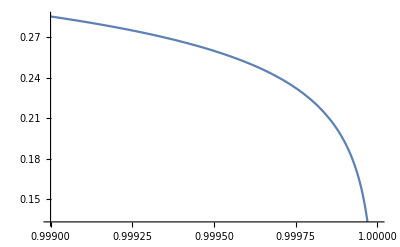

```mathematica
Plot[ϕ1'[x],{x,1-0.001,1}]
```

```mathematica
?ϕ1
```

Global`ϕ1

ϕ1=ϕn[0][ΦB]
 
ϕ1[x_]=2.00661 (0.343526 (1-x)^1.06207 x^0.937928+0.346584 (1-x)^0.937928 x^1.06207-0.841569 Sin[π x]+0.000042429 Sin[2 π x]+0.230083 Sin[3 π x]+9.86781×10^-6 Sin[4 π x]-0.0263305 Sin[5 π x]+4.64373×10^-6 Sin[6 π x]+0.000548951 Sin[7 π x]+3.68061×10^-6 Sin[8 π x])

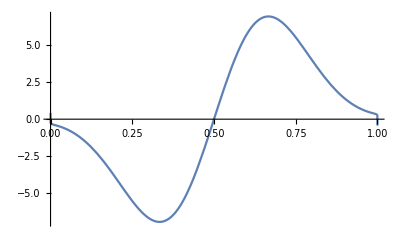

```mathematica
Plot[ϕ1'[x],{x,0,1}]
```

```mathematica
Table[ϕ1'[10^-i],{i,1,10}]
```

{-1.39576,-0.379082,-0.287859,-0.196612,-0.0759039,0.0789745,0.271424,0.505408,0.785716,1.11809}

```mathematica
Limit[Boole[0<x<1]ϕ1'[x],x->0]
```

Indeterminate

```mathematica
ϕ1'[x]
```

2.00661 ((0.322203 (1-x)^1.06207)/x^0.062072+0.368098 (1-x)^0.937928 x^0.062072-0.364849 (1-x)^0.062072 x^0.937928-(0.325071 x^1.06207)/(1-x)^0.062072-2.64387 Cos[π x]+0.000266589 Cos[2 π x]+2.16848 Cos[3 π x]+0.000124003 Cos[4 π x]-0.413599 Cos[5 π x]+0.0000875323 Cos[6 π x]+0.0120721 Cos[7 π x]+0.0000925039 Cos[8 π x])

```mathematica
Limit[ϕp1[x],x->0]
```

Indeterminate

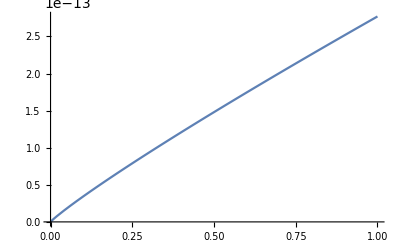

```mathematica
Plot[ϕ1[x],{x,0,0.0000000000001}]
```